```mathematica
<<"green.txt"
```

0

-(w1-w2)^2/(4 (tau Vt^2) nu)+(4 ⅈ omega tau Vt^2-4 ⅈ omega0 tau Vt^2+(-2 ⅈ kp tau Vt^2-w1+w2) (w1+w2))/(4 Vt^2)-((tau (kp^2 tau^2 Vt^4+w1^2+w1 w2+w2^2)) nu)/(12 Vt^2)+O[nu]^2

If[Im[omega]>kp Im[w],-ⅈ/(-omega+omega0+kp w),Integrate[ⅇ^(ⅈ tau (omega-omega0-kp w)),{tau,0,∞},Assumptions→(omega0|kp|nu|Vt|tau)∈Reals&&nu>0&&Vt>0&&(kp Im[w]≥Im[omega]||Im[omega-kp w]≤0)]]

```mathematica
G[w1,w2,tau,nu]
```

(ⅇ^(-tau (ⅈ (-omega+omega0)+(kp^2 Vt^2)/nu)+(ⅈ kp (w1-w2))/nu-(((2 ⅈ (1-ⅇ^(-nu tau)) kp Vt^2)/nu+w1-ⅇ^(-nu tau) w2)^2)/(2 (1-ⅇ^(-2 nu tau)) Vt^2)))/(√(2 π) √((1-ⅇ^(-2 nu tau)) Vt^2))

```mathematica
FullSimplify[G[w1,w2,tau,nu] Exp[-1/2 w2^2/Vt^2]]
```

(ⅇ^(-tau (ⅈ (-omega+omega0)+(kp^2 Vt^2)/nu)+(ⅈ kp (w1-w2))/nu-w2^2/(2 Vt^2)-((2 ⅈ (-1+ⅇ^(nu tau)) kp Vt^2+nu (ⅇ^(nu tau) w1-w2))^2 (-1+Coth[nu tau]))/(4 nu^2 Vt^2)))/(√(1-ⅇ^(-2 nu tau)) √(2 π) Vt)

```mathematica
Expand[argG[w1,w2,tau,nu]-1/2 w2^2/Vt^2]
```

ⅈ omega tau-ⅈ omega0 tau+(2 kp^2 Vt^2)/((1-ⅇ^(-2 nu tau)) nu^2)+(2 ⅇ^(-2 nu tau) kp^2 Vt^2)/((1-ⅇ^(-2 nu tau)) nu^2)-(4 ⅇ^(-nu tau) kp^2 Vt^2)/((1-ⅇ^(-2 nu tau)) nu^2)-(kp^2 tau Vt^2)/nu+(ⅈ kp w1)/nu-(2 ⅈ kp w1)/((1-ⅇ^(-2 nu tau)) nu)+(2 ⅈ ⅇ^(-nu tau) kp w1)/((1-ⅇ^(-2 nu tau)) nu)-w1^2/(2 (1-ⅇ^(-2 nu tau)) Vt^2)-(ⅈ kp w2)/nu-(2 ⅈ ⅇ^(-2 nu tau) kp w2)/((1-ⅇ^(-2 nu tau)) nu)+(2 ⅈ ⅇ^(-nu tau) kp w2)/((1-ⅇ^(-2 nu tau)) nu)+(ⅇ^(-nu tau) w1 w2)/((1-ⅇ^(-2 nu tau)) Vt^2)-w2^2/(2 Vt^2)-(ⅇ^(-2 nu tau) w2^2)/(2 (1-ⅇ^(-2 nu tau)) Vt^2)

```mathematica
FullSimplify[G[w1,w2,tau,nu] Exp[-1/2 w2^2/Vt^2]-G[w2,w1,tau,nu] Exp[-1/2 w1^2/Vt^2]]
```

0

```mathematica
<<"W2_func.txt";
```

0

√(2 π) Vt If[Im[omega]>0||kp≠0,(ⅇ^(-(omega-omega0)^2/(2 kp^2 Vt^2)) √(π/2) (Abs[kp]+ⅈ kp Erfi[(omega-omega0)/(√2 kp Vt)]))/(kp^2 Vt),Integrate[ⅇ^(-1/2 tau (-2 ⅈ omega+2 ⅈ omega0+kp^2 tau Vt^2)),{tau,0,∞},Assumptions→omega0∈Reals&&tau∈Reals&&Im[omega]≤0&&Vt>0&&nu>0&&kp==0]]

-ⅈ kp √(2 π) Vt^3 If[Im[omega]>0||kp≠0,(ⅇ^(-(omega-omega0)^2/(2 kp^2 Vt^2)) (2 ⅇ^((omega-omega0)^2/(2 kp^2 Vt^2)) √(-kp^4 (omega-omega0)^2 Vt^4)+(omega-omega0) √(2 π) Vt Abs[kp] (ⅈ √(-(omega-omega0)^2)+(-omega+omega0) Erf[(√(-(omega-omega0)^2/(kp^2 Vt^2)))/(√2)])))/(2 kp^4 √(-(omega-omega0)^2) Vt^4),Integrate[ⅇ^(-1/2 tau (-2 ⅈ omega+2 ⅈ omega0+kp^2 tau Vt^2)) tau,{tau,0,∞},Assumptions→omega0∈Reals&&tau∈Reals&&Im[omega]≤0&&Vt>0&&nu>0&&kp==0]]

If[Im[omega]>0||kp≠0,-(ⅇ^(-(omega-omega0)^2/(2 kp^2 Vt^2)) √(π/2) (-2 ⅈ ⅇ^((omega-omega0)^2/(2 kp^2 Vt^2)) kp^2 (omega-omega0)^2 Vt Abs[kp]+4 ⅈ ⅇ^((omega-omega0)^2/(2 kp^2 Vt^2)) (omega-omega0)^2 Vt Abs[kp]^3+kp^2 √(2 π) (-(omega-omega0)^3+ⅈ (omega^2 √(-(omega-omega0)^2)-2 omega √(-(omega-omega0)^2) omega0+√(-(omega-omega0)^2) omega0^2-kp^2 √(-(omega-omega0)^2) Vt^2+√(-kp^4 (omega-omega0)^2 Vt^4)) Erf[(√(-(omega-omega0)^2/(kp^2 Vt^2)))/(√2)])))/(kp^2 (omega-omega0) Abs[kp]^3),Integrate[ⅇ^(-1/2 tau (-2 ⅈ omega+2 ⅈ omega0+kp^2 tau Vt^2)) √(2 π) Vt^3-ⅇ^(-1/2 tau (-2 ⅈ omega+2 ⅈ omega0+kp^2 tau Vt^2)) kp^2 √(2 π) tau^2 Vt^5,{tau,0,∞},Assumptions→omega0∈Reals&&tau∈Reals&&Im[omega]≤0&&Vt>0&&nu>0&&kp==0]]

0

General::obspkg: Algebra`Horner` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

-(ⅈ sqrt2p nu[1] Vt[1] (-dom[2] nu[2]+2 nu[4]+5 kp[2] nu[2] Vt[2]-3 ⅈ dom[1] (nu[3]+kp[2] nu[1] Vt[2])+(3+F11m) kp[4] Vt[4]))/((dom[1] nu[1]+ⅈ kp[2] Vt[2]) (dom[1] nu[1]+ⅈ (nu[2]+kp[2] Vt[2])) (dom[1] nu[1]+ⅈ (2 nu[2]+kp[2] Vt[2])))

-(ⅈ sqrt2p kp[1] Vt[3] (dom[1] (-nu[3]+F11m kp[2] nu[1] Vt[2])-ⅈ (2 nu[4]+3 kp[2] nu[2] Vt[2]+kp[4] Vt[4])))/((dom[1] nu[1]+ⅈ kp[2] Vt[2]) (dom[1] nu[1]+ⅈ (nu[2]+kp[2] Vt[2])) (dom[1] nu[1]+ⅈ (2 nu[2]+kp[2] Vt[2])))

-(sqrt2p (dom[1]+ⅈ nu[1]) Vt[3] (2 nu[4]+3 kp[2] nu[2] Vt[2]-ⅈ dom[1] (nu[3]-F11m kp[2] nu[1] Vt[2])+kp[4] Vt[4]))/((dom[1] nu[1]+ⅈ kp[2] Vt[2]) (dom[1] nu[1]+ⅈ (nu[2]+kp[2] Vt[2])) (dom[1] nu[1]+ⅈ (2 nu[2]+kp[2] Vt[2])))

-(sqrt2p kp[1] (ⅈ F11m dom[3] nu[1]-ⅈ (3+2 F11m) dom[1] nu[3]+6 nu[4]+(7+2 F11m) kp[2] nu[2] Vt[2]+dom[2] (-3 F11m nu[2]+kp[2] Vt[2])+kp[4] Vt[4]) Vt[5])/((dom[1] nu[1]+ⅈ (2 nu[2]+kp[2] Vt[2])) (dom[2] nu[2]-kp[2] Vt[2] (nu[2]+kp[2] Vt[2])+ⅈ dom[1] (nu[3]+2 kp[2] nu[1] Vt[2])))

-(ⅈ sqrt2p kp[1] Vt[3] (dom[1] (-nu[3]+F11m kp[2] nu[1] Vt[2])-ⅈ (2 nu[4]+3 kp[2] nu[2] Vt[2]+kp[4] Vt[4])))/((dom[1] nu[1]+ⅈ kp[2] Vt[2]) (dom[1] nu[1]+ⅈ (nu[2]+kp[2] Vt[2])) (dom[1] nu[1]+ⅈ (2 nu[2]+kp[2] Vt[2])))

-(ⅈ sqrt2p dom[1] Vt[3] (dom[1] (-nu[3]+F11m kp[2] nu[1] Vt[2])-ⅈ (2 nu[4]+3 kp[2] nu[2] Vt[2]+kp[4] Vt[4])))/((dom[1] nu[1]+ⅈ kp[2] Vt[2]) (dom[1] nu[1]+ⅈ (nu[2]+kp[2] Vt[2])) (dom[1] nu[1]+ⅈ (2 nu[2]+kp[2] Vt[2])))

-(sqrt2p kp[1] (ⅈ F11m dom[3] nu[1]+2 nu[4]+3 kp[2] nu[2] Vt[2]+dom[2] (-F11m nu[2]+kp[2] Vt[2])-ⅈ dom[1] (3 nu[3]+2 kp[2] nu[1] Vt[2])+kp[4] Vt[4]) Vt[5])/((dom[1] nu[1]+ⅈ (2 nu[2]+kp[2] Vt[2])) (dom[2] nu[2]-kp[2] Vt[2] (nu[2]+kp[2] Vt[2])+ⅈ dom[1] (nu[3]+2 kp[2] nu[1] Vt[2])))

(sqrt2p dom[1] (-ⅈ F11m dom[3] nu[1]+ⅈ (3+2 F11m) dom[1] nu[3]-6 nu[4]-(7+2 F11m) kp[2] nu[2] Vt[2]+dom[2] (3 F11m nu[2]-kp[2] Vt[2])-kp[4] Vt[4]) Vt[5])/((dom[1] nu[1]+ⅈ (2 nu[2]+kp[2] Vt[2])) (dom[2] nu[2]-kp[2] Vt[2] (nu[2]+kp[2] Vt[2])+ⅈ dom[1] (nu[3]+2 kp[2] nu[1] Vt[2])))

General::obspkg: Algebra`Horner` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

0, 0, (ⅈ √(π/2) Vt (2+2 Wm z[-4]+z[-2]))/dom

0, 1, (ⅈ √π Vt^2 (2 Wm z[-3]+z[-1]))/dom

0, 2, (ⅈ √(2 π) Vt^3 (1+2 Wm z[-2]))/dom

0, 3, (4 ⅈ √π Vt^4 Wm z[-1])/dom

1, 0, (ⅈ √π Vt^2 (2 Wm z[-3]+z[-1]))/dom

1, 1, (ⅈ √(2 π) Vt^3 (1+2 Wm z[-2]))/dom

1, 2, (4 ⅈ √π Vt^4 Wm z[-1])/dom

1, 3, (4 ⅈ √(2 π) Vt^5 Wm)/dom

```mathematica
S={{omc^2 Wf[0,0],omc Vth Wf[0,0]+omc hth Wf[0,1],omc Vz Wf[0,0]+omc hz Wf[0,1]},{Vth omc Wf[0,0]+hth omc Wf[0,1],Vth^2 Wf[0,0]+2hth Vth Wf[0,1]+hth^2 Wf[1,1],Vth Vz Wf[0,0]+(hth Vz+hz Vth) Wf[0,1]+hth hz Wf[1,1]},{Vz omc Wf[0,0]+hz omc Wf[0,1],Vth Vz Wf[0,0]+(hth Vz+hz Vth) Wf[0,1]+hth hz Wf[1,1],Vz^2Wf[0,0]+2hz Vz Wf[0,1]+hz^2Wf[1,1]}}
```

{{omc^2 Wf[0,0],omc Vth Wf[0,0]+hth omc Wf[0,1],omc Vz Wf[0,0]+hz omc Wf[0,1]},{omc Vth Wf[0,0]+hth omc Wf[0,1],Vth^2 Wf[0,0]+2 hth Vth Wf[0,1]+hth^2 Wf[1,1],Vth Vz Wf[0,0]+(hz Vth+hth Vz) Wf[0,1]+hth hz Wf[1,1]},{omc Vz Wf[0,0]+hz omc Wf[0,1],Vth Vz Wf[0,0]+(hz Vth+hth Vz) Wf[0,1]+hth hz Wf[1,1],Vz^2 Wf[0,0]+2 hz Vz Wf[0,1]+hz^2 Wf[1,1]}}

```mathematica
MatrixForm[S]
```

(omc^2 Wf[0,0] | omc Vth Wf[0,0]+hth omc Wf[0,1] | omc Vz Wf[0,0]+hz omc Wf[0,1]
omc Vth Wf[0,0]+hth omc Wf[0,1] | Vth^2 Wf[0,0]+2 hth Vth Wf[0,1]+hth^2 Wf[1,1] | Vth Vz Wf[0,0]+(hz Vth+hth Vz) Wf[0,1]+hth hz Wf[1,1]
omc Vz Wf[0,0]+hz omc Wf[0,1] | Vth Vz Wf[0,0]+(hz Vth+hth Vz) Wf[0,1]+hth hz Wf[1,1] | Vz^2 Wf[0,0]+2 hz Vz Wf[0,1]+hz^2 Wf[1,1])

```mathematica
L=Eigenvalues[S]
```

{0,1/(2 r0^2)(omc^2 r0^2 Wf[0,0]+r0^2 Vth^2 Wf[0,0]+Vz^2 Wf[0,0]+2 hth r0^2 Vth Wf[0,1]+2 hz Vz Wf[0,1]+hz^2 Wf[1,1]+hth^2 r0^2 Wf[1,1]-√((-omc^2 r0^2 Wf[0,0]-r0^2 Vth^2 Wf[0,0]-Vz^2 Wf[0,0]-2 hth r0^2 Vth Wf[0,1]-2 hz Vz Wf[0,1]-hz^2 Wf[1,1]-hth^2 r0^2 Wf[1,1])^2-4 r0^2 (-hz^2 omc^2 Wf[0,1]^2-hth^2 omc^2 r0^2 Wf[0,1]^2-hz^2 Vth^2 Wf[0,1]^2+2 hth hz Vth Vz Wf[0,1]^2-hth^2 Vz^2 Wf[0,1]^2+hz^2 omc^2 Wf[0,0] Wf[1,1]+hth^2 omc^2 r0^2 Wf[0,0] Wf[1,1]+hz^2 Vth^2 Wf[0,0] Wf[1,1]-2 hth hz Vth Vz Wf[0,0] Wf[1,1]+hth^2 Vz^2 Wf[0,0] Wf[1,1]))),1/(2 r0^2)(omc^2 r0^2 Wf[0,0]+r0^2 Vth^2 Wf[0,0]+Vz^2 Wf[0,0]+2 hth r0^2 Vth Wf[0,1]+2 hz Vz Wf[0,1]+hz^2 Wf[1,1]+hth^2 r0^2 Wf[1,1]+√((-omc^2 r0^2 Wf[0,0]-r0^2 Vth^2 Wf[0,0]-Vz^2 Wf[0,0]-2 hth r0^2 Vth Wf[0,1]-2 hz Vz Wf[0,1]-hz^2 Wf[1,1]-hth^2 r0^2 Wf[1,1])^2-4 r0^2 (-hz^2 omc^2 Wf[0,1]^2-hth^2 omc^2 r0^2 Wf[0,1]^2-hz^2 Vth^2 Wf[0,1]^2+2 hth hz Vth Vz Wf[0,1]^2-hth^2 Vz^2 Wf[0,1]^2+hz^2 omc^2 Wf[0,0] Wf[1,1]+hth^2 omc^2 r0^2 Wf[0,0] Wf[1,1]+hz^2 Vth^2 Wf[0,0] Wf[1,1]-2 hth hz Vth Vz Wf[0,0] Wf[1,1]+hth^2 Vz^2 Wf[0,0] Wf[1,1])))}

```mathematica
Tr[S]
```

omc^2 Wf[0,0]+Vth^2 Wf[0,0]+2 hth Vth Wf[0,1]+hth^2 Wf[1,1]+(Vz^2 Wf[0,0]+2 hz Vz Wf[0,1]+hz^2 Wf[1,1])/r0^2

```mathematica
Det[S]
```

0

```mathematica
Simplify[L[[3]]+L[[2]]-L[[2]]/.Wf->Wfwc,Assumptions->Element[{Vt,omega,omega0,kp,nu},Reals] &&kp>0 &&Vt>0 && nu>0]
```

1/(kp^2 nu r0^2)ⅇ^((kp^2 Vt^2)/nu^2) √(π/2) Vt (√(hz^2 (omega-omega0)^2+hth^2 (omega-omega0)^2 r0^2+2 hth kp (omega-omega0) r0^2 Vth+2 hz kp (omega-omega0) Vz+kp^2 (omc^2 r0^2+r0^2 Vth^2+Vz^2))^2 Abs[Re[((kp Vt)/nu)^((2 ⅈ (nu (omega-omega0)+ⅈ kp^2 Vt^2))/nu^2) (Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2]-Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2,(kp^2 Vt^2)/nu^2])]]+(hz^2 (omega-omega0)^2+hth^2 (omega-omega0)^2 r0^2+2 hth kp (omega-omega0) r0^2 Vth+2 hz kp (omega-omega0) Vz+kp^2 (omc^2 r0^2+r0^2 Vth^2+Vz^2)) Re[((kp Vt)/nu)^((2 ⅈ (nu (omega-omega0)+ⅈ kp^2 Vt^2))/nu^2) (Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2]-Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2,(kp^2 Vt^2)/nu^2])])

```mathematica
Simplify[L[[2]]*L[[3]]]
```

-(hz^2 (omc^2+Vth^2)-2 hth hz Vth Vz+hth^2 (omc^2+Vz^2)) (Wf[0,1]^2-Wf[0,0] Wf[1,1])

```mathematica
W00=FullSimplify[J1der[0,0,nu]]
```

1/nu ⅇ^((kp^2 Vt^2)/nu^2) √(2 π) Vt ((kp^2 Vt^2)/nu^2)^((ⅈ nu (omega-omega0)-kp^2 Vt^2)/nu^2) (Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2]-Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2,(kp^2 Vt^2)/nu^2])

```mathematica
FullSimplify[(Re[J1derNC[0,1,nu]])^2-Re[J1derNC[0,0,nu]]Re[J1derNC[1,1,nu]]]
```

$Aborted

```mathematica
J1derNC[1,1,nu]
```

1/(kp^4 Abs[kp])(omega-omega0) (-ⅈ √(2 π) Vt Abs[kp]^3+ⅇ^(-(omega-omega0)^2/(2 kp^2 Vt^2)) kp (omega-omega0) π (kp+ⅈ Abs[kp] Erfi[(omega-omega0)/(√2 kp Vt)]))

```mathematica
JLimT=Sqrt[2*Pi]*Vt*((1/(Vt*Abs[kp]))*(E^(((omega-omega0)*(-omega+omega0+2*(alpha+beta)*kp*Vt^2))/(2*kp^2*Vt^2))*Sqrt[Pi/2]*(1-I*Erfi[((-omega+omega0+(alpha+beta)*kp*Vt^2)*Abs[kp])/(Sqrt[2]*kp^2*Vt)])));
```

```mathematica
a1=FullSimplify[(Re[J1derNC[0,1,nu]])^2,Assumptions->{Element[{Vt,omega,omega0,kp},Reals],kp>0,Vt>0}]
```

(ⅇ^(-(omega-omega0)^2/(kp^2 Vt^2)) (omega-omega0)^2 π^2)/kp^4

```mathematica
FullSimplify[(Re[J1derNC[0,1,nu]])^2-Re[J1derNC[0,0,nu]]Re[J1derNC[1,1,nu]],Assumptions->{Element[{Vt,omega,omega0,kp},Reals],kp>0,Vt>0}]
```

0

```mathematica
a2=FullSimplify[Re[J1derNC[0,0,nu]],Assumptions->{Element[{Vt,omega,omega0,kp},Reals],kp>0,Vt>0}]
```

(ⅇ^(-(omega-omega0)^2/(2 kp^2 Vt^2)) π)/kp

```mathematica
a3=FullSimplify[Re[J1derNC[1,1,nu]],Assumptions->{Element[{Vt,omega,omega0,kp},Reals],kp>0,Vt>0}]
```

(ⅇ^(-(omega-omega0)^2/(2 kp^2 Vt^2)) (omega-omega0)^2 π)/kp^3

```mathematica
a1-a2*a3
```

0

```mathematica
TT=Simplify[L[[3]]/.Wf->Wfwc,Assumptions->Element[{Vt,omega,omega0,kp,Vth,Vz,omc,hth,hz,nu},Reals] &&kp>0&&Vt>0 && nu>0]
```

1/(kp^2 nu)ⅇ^((kp^2 Vt^2)/nu^2) √(π/2) Vt (Abs[(hth^2+hz^2) (omega-omega0)^2+2 kp (omega-omega0) (hth Vth+hz Vz)+kp^2 (omc^2+Vth^2+Vz^2)] Abs[Re[((kp Vt)/nu)^((2 ⅈ (nu (omega-omega0)+ⅈ kp^2 Vt^2))/nu^2) (Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2]-Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2,(kp^2 Vt^2)/nu^2])]]+((hth^2+hz^2) (omega-omega0)^2+2 kp (omega-omega0) (hth Vth+hz Vz)+kp^2 (omc^2+Vth^2+Vz^2)) Re[((kp Vt)/nu)^((2 ⅈ (nu (omega-omega0)+ⅈ kp^2 Vt^2))/nu^2) (Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2]-Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2,(kp^2 Vt^2)/nu^2])])

```mathematica
Simplify[L[[2]]/.Wf->Wfwc,Assumptions->Element[{Vt,omega,omega0,kp,Vth,Vz,omc,hth,hz,nu},Reals] &&kp>0 &&Vt>0 && nu>0]
```

-1/(kp^2 nu)ⅇ^((kp^2 Vt^2)/nu^2) √(π/2) Vt (Abs[(hth^2+hz^2) (omega-omega0)^2+2 kp (omega-omega0) (hth Vth+hz Vz)+kp^2 (omc^2+Vth^2+Vz^2)] Abs[Re[((kp Vt)/nu)^((2 ⅈ (nu (omega-omega0)+ⅈ kp^2 Vt^2))/nu^2) (Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2]-Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2,(kp^2 Vt^2)/nu^2])]]-((hth^2+hz^2) (omega-omega0)^2+2 kp (omega-omega0) (hth Vth+hz Vz)+kp^2 (omc^2+Vth^2+Vz^2)) Re[((kp Vt)/nu)^((2 ⅈ (nu (omega-omega0)+ⅈ kp^2 Vt^2))/nu^2) (Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2]-Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2,(kp^2 Vt^2)/nu^2])])

```mathematica
Wfnc[m1_,n1_]:=Re[J1derNC[m1,n1,nu]];
Wfwc[m1_,n1_]:=Re[J1der[m1,n1,nu]];
```

```mathematica
L[[2]]
```

1/2 (omc^2 Wf[0,0]+Vth^2 Wf[0,0]+Vz^2 Wf[0,0]+2 hth Vth Wf[0,1]+2 hz Vz Wf[0,1]+hth^2 Wf[1,1]+hz^2 Wf[1,1]-√((-omc^2 Wf[0,0]-Vth^2 Wf[0,0]-Vz^2 Wf[0,0]-2 hth Vth Wf[0,1]-2 hz Vz Wf[0,1]-hth^2 Wf[1,1]-hz^2 Wf[1,1])^2-4 (-hth^2 omc^2 Wf[0,1]^2-hz^2 omc^2 Wf[0,1]^2-hz^2 Vth^2 Wf[0,1]^2+2 hth hz Vth Vz Wf[0,1]^2-hth^2 Vz^2 Wf[0,1]^2+hth^2 omc^2 Wf[0,0] Wf[1,1]+hz^2 omc^2 Wf[0,0] Wf[1,1]+hz^2 Vth^2 Wf[0,0] Wf[1,1]-2 hth hz Vth Vz Wf[0,0] Wf[1,1]+hth^2 Vz^2 Wf[0,0] Wf[1,1])))

```mathematica
Simplify[Wf[0,1]/.Wf->Wfwc,Assumptions->Element[{Vt,omega,omega0,kp,nu},Reals] &&kp>0 &&Vt>0 && nu>0]
```

1/(kp nu)ⅇ^((kp^2 Vt^2)/nu^2) (omega-omega0) √(2 π) Vt Re[((kp Vt)/nu)^((2 ⅈ (nu (omega-omega0)+ⅈ kp^2 Vt^2))/nu^2) (Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2]-Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2,(kp^2 Vt^2)/nu^2])]

```mathematica
Wfnc[1,0]
```

Re[(-ⅈ √(2 π) Vt+(ⅇ^(-(omega-omega0)^2/(2 kp^2 Vt^2)) (omega-omega0) π (1+ⅈ Erfi[((omega-omega0) Abs[kp])/(√2 kp^2 Vt)]))/Abs[kp])/kp]

```mathematica
Simplify[(Re[J1der[0,1,nu]])^2-Re[J1der[0,0,nu]]Re[J1der[1,1,nu]],Assumptions->Element[{Vt,omega,omega0,kp,nu},Reals] &&kp>0 &&Vt>0 && nu>0]
```

0

```mathematica
(Re[J1derNC[0,1,nu]])^2-Re[J1derNC[0,0,nu]]Re[J1derNC[1,1,nu]]
```

```mathematica
Simplify[L[[2]] L[[3]]/.Wf->Wfwc,Assumptions->Element[{Vt,omega,omega0,kp,nu},Reals] &&kp>0 &&Vt>0 && nu>0]
```

0

```mathematica
test=Simplify[Tr[S]/.Wf->Wfwc,Assumptions->Element[{Vt,omega,omega0,kp,nu},Reals] &&kp>0 &&Vt>0 && nu>0]
```

1/(kp^2 nu r0^2)ⅇ^((kp^2 Vt^2)/nu^2) √(2 π) Vt ((omega-omega0) (hz^2 (omega-omega0)+hth r0^2 (hth (omega-omega0)+2 kp Vth)+2 hz kp Vz)+kp^2 (omc^2 r0^2+r0^2 Vth^2+Vz^2)) Re[((kp Vt)/nu)^((2 ⅈ (nu (omega-omega0)+ⅈ kp^2 Vt^2))/nu^2) (Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2]-Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2,(kp^2 Vt^2)/nu^2])]

```mathematica
res=ReplaceRepeated[test,{Sqrt[2*Pi]->sqrt2p,kp^2*Vt^2/nu^2->t1,(-I*nu*(omega-omega0)+kp^2*Vt^2)/nu^2->t2,(I*nu*(omega-omega0)-kp^2*Vt^2)/nu^2->-t2,Gamma[t2]->Gamma[t2,t1]+gam,Exp[t1]->Ex,t1^(-t2)->1/t1Pt2,omega-omega0->dom}];

res=Simplify[ReplaceAll[res,{gam->1/Ex*t1Pt2/t2*F11}]]
(*Print[res];*)
res=Simplify[ReplaceRepeated[res,{t2->t1-I dom/nu,t1->kp^2*Vt^2/nu^2,omega->dom+omega0}]];
res=ReplaceRepeated[res,{Sqrt[2*Pi]->sqrt2p,kp^2*Vt^2/nu^2->t1,(-I*nu*(omega-omega0)+kp^2*Vt^2)/nu^2->t2,(I*nu*(omega-omega0)-kp^2*Vt^2)/nu^2->-t2,Gamma[t2]->Gamma[t2,t1]+gam,Exp[t1]->Ex,t1^(-t2)->1/t1Pt2,omega-omega0->dom}]
```

1/(kp^2 nu r0^2)Ex sqrt2p Vt (dom (dom hz^2+hth r0^2 (dom hth+2 kp Vth)+2 hz kp Vz)+kp^2 (omc^2 r0^2+r0^2 Vth^2+Vz^2)) Re[(F11 t1Pt2 ((kp Vt)/nu)^((2 ⅈ dom nu-2 kp^2 Vt^2)/nu^2))/(Ex t2)]

-1/(kp^2 nu r0^2)Ex sqrt2p Vt (dom (dom hz^2+hth r0^2 (dom hth+2 kp Vth)+2 hz kp Vz)+kp^2 (omc^2 r0^2+r0^2 Vth^2+Vz^2)) Im[(F11 nu^2 t1Pt2 ((kp Vt)/nu)^((2 ⅈ dom nu-2 kp^2 Vt^2)/nu^2))/(Ex (dom nu+ⅈ kp^2 Vt^2))]

```mathematica
qq=N[Re[Simplify[Hypergeometric1F1[1,1+t1+I d,t1]/(t1+I d),Assumptions->t1>0]],20]
```

Re[Hypergeometric1F1[1.,(1.+1. ⅈ)+t1,t1]/(1. ⅈ+t1)]

```mathematica
N[qq/.{t1->10,d->10},20]
```

Re[(0.0990099-0.00990099 ⅈ) Hypergeometric1F1[1.,11.+1. ⅈ,10.]]

```mathematica
]
```

Re[Hypergeometric1F1[1,1+ⅈ d+t1,t1]/(ⅈ d+t1)]

```mathematica
Clear[t1,t2]
```

```mathematica
Re[Hypergeometric1F1[1,1+t2,t1]/t2
```

```mathematica
qq
```

Re[(0.5-0.5 ⅈ) Hypergeometric1F1[1.,2.+1. ⅈ,1.]]

```mathematica
Eval
```

```mathematica
pp[t1_,t3_]:=Re[Hypergeometric1F1[1,1+t1+I t3,t1]/(t1+I t3)]
```

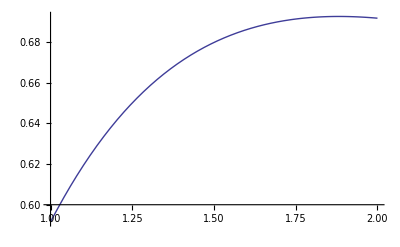

-Graphics-

```mathematica
Plot[pp[t1,t3]/.t3->1,{t1,1,2}]
```

```mathematica
Plot3D[pp[t1,t3],{t1,0,10^5},{t3,-10^4,10^4}]
```

-Graphics3D-

```mathematica
Simplify[Re[J1der[0,0,nu]],Assumptions->Element[{Vt,omega,omega0,kp,nu},Reals] &&kp>0 &&Vt>0 && nu>0]
```

1/nu ⅇ^((kp^2 Vt^2)/nu^2) √(2 π) Vt Re[((kp Vt)/nu)^((2 ⅈ (nu (omega-omega0)+ⅈ kp^2 Vt^2))/nu^2) (Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2]-Gamma[(-ⅈ nu (omega-omega0)+kp^2 Vt^2)/nu^2,(kp^2 Vt^2)/nu^2])]

```mathematica
pp=FullSimplify[G[w1,w2,tau,nu] Exp[-1/2 w2^2/Vt^2]]
```

(ⅇ^(-tau (ⅈ (-omega+omega0)+(kp^2 Vt^2)/nu)+(ⅈ kp (w1-w2))/nu-w2^2/(2 Vt^2)-((2 ⅈ (-1+ⅇ^(nu tau)) kp Vt^2+nu (ⅇ^(nu tau) w1-w2))^2 (-1+Coth[nu tau]))/(4 nu^2 Vt^2)))/(√(1-ⅇ^(-2 nu tau)) √(2 π) Vt)

```mathematica
EE=x^2+y^2-a x y+b(x+y)
```

x^2-a x y+y^2+b (x+y)

```mathematica
Simplify[EE/.{x->Sqrt[2]/2 (u1-u2),y->Sqrt[2]/2 (u1+u2)}]
```

√2 b u1+1/2 (-(-2+a) u1^2+(2+a) u2^2)

```mathematica
Simplify[argG[w1,w2,tau,nu]-1/2 w2^2/Vt^2-1/4/a[tau,nu](b[tau,nu]*b[tau,nu]-4a[tau,nu]c[tau,nu]-w1^2-w2^2+2Exp[-nu tau]w1 w2-2Vt^2 kp I/nu(1-Exp[-nu tau])^2(w1+w2))]
```

0

```mathematica
Simplify[1/4/a[tau,nu](b[tau,nu]*b[tau,nu]-4a[tau,nu]c[tau,nu]-w1^2-w2^2+2Exp[-nu tau]w1 w2-2Vt^2 kp I/nu(1-Exp[-nu tau])^2(w1+w2))]
```

-1/(2 (1-ⅇ^(-2 nu tau)) Vt^2)(-(4 (kp-ⅇ^(-nu tau) kp)^2 Vt^4)/nu^2+2 (1-ⅇ^(-2 nu tau)) tau Vt^2 (ⅈ (-omega+omega0)+(kp^2 Vt^2)/nu)+w1^2-2 ⅇ^(-nu tau) w1 w2+w2^2+(2 ⅈ kp (Vt-ⅇ^(-nu tau) Vt)^2 (w1+w2))/nu)

```mathematica
S={{omc^2 Wf[0,0],omc Vth Wf[0,0]+omc hth Wf[0,1],r0^(-1)(omc Vz Wf[0,0]+omc hz Wf[0,1])},{Vth omc Wf[0,0]+hth omc Wf[0,1],Vth^2 Wf[0,0]+2hth Vth Wf[0,1]+hth^2 Wf[1,1],r0^(-1)(Vth Vz Wf[0,0]+(hth Vz+hz Vth) Wf[0,1]+hth hz Wf[1,1])},{r0^(-1)(Vz omc Wf[0,0]+hz omc Wf[0,1]),r0^(-1)(Vth Vz Wf[0,0]+(hth Vz+hz Vth) Wf[0,1]+hth hz Wf[1,1]),r0^(-2)(Vz^2Wf[0,0]+2hz Vz Wf[0,1]+hz^2Wf[1,1])}}
```

{{omc^2 Wf[0,0],omc Vth Wf[0,0]+hth omc Wf[0,1],(omc Vz Wf[0,0]+hz omc Wf[0,1])/r0},{omc Vth Wf[0,0]+hth omc Wf[0,1],Vth^2 Wf[0,0]+2 hth Vth Wf[0,1]+hth^2 Wf[1,1],(Vth Vz Wf[0,0]+(hz Vth+hth Vz) Wf[0,1]+hth hz Wf[1,1])/r0},{(omc Vz Wf[0,0]+hz omc Wf[0,1])/r0,(Vth Vz Wf[0,0]+(hz Vth+hth Vz) Wf[0,1]+hth hz Wf[1,1])/r0,(Vz^2 Wf[0,0]+2 hz Vz Wf[0,1]+hz^2 Wf[1,1])/r0^2}}

```mathematica
MatrixForm[S]
```

(omc^2 Wf[0,0] | omc Vth Wf[0,0]+hth omc Wf[0,1] | (omc Vz Wf[0,0]+hz omc Wf[0,1])/r0
omc Vth Wf[0,0]+hth omc Wf[0,1] | Vth^2 Wf[0,0]+2 hth Vth Wf[0,1]+hth^2 Wf[1,1] | (Vth Vz Wf[0,0]+(hz Vth+hth Vz) Wf[0,1]+hth hz Wf[1,1])/r0
(omc Vz Wf[0,0]+hz omc Wf[0,1])/r0 | (Vth Vz Wf[0,0]+(hz Vth+hth Vz) Wf[0,1]+hth hz Wf[1,1])/r0 | (Vz^2 Wf[0,0]+2 hz Vz Wf[0,1]+hz^2 Wf[1,1])/r0^2)

```mathematica
tt=Tr[S]
```

omc^2 Wf[0,0]+Vth^2 Wf[0,0]+2 hth Vth Wf[0,1]+hth^2 Wf[1,1]+(Vz^2 Wf[0,0]+2 hz Vz Wf[0,1]+hz^2 Wf[1,1])/r0^2

```mathematica
T = List[{{a,b},{c,d}}]
```

{{{a,b},{c,d}}}

```mathematica
MatrixForm[Inverse[T]]
```

Inverse::matsq: Argument {{{a, b}, {c, d}}} at position 1 is not a non-empty square matrix.

```mathematica
Inverse[{{a,b},{c,d}}]
```

{{d/(-b c+a d),-b/(-b c+a d)},{-c/(-b c+a d),a/(-b c+a d)}}